# Feedforward neural network - classification

## Loading of package and data

```mathematica
<<NeuralNets`
```

```mathematica
trainingData=ExampleData[{"MachineLearning","FisherIris"},"TrainingData"];testData=ExampleData[{"MachineLearning","FisherIris"},"TestData"];
```

```mathematica
xTrain=#[[1]]&/@trainingData;
yTrain=(#[[2]]/.{"setosa"->{1,0,0},"versicolor"->{0,1,0},"virginica"->{0,0,1}})&/@trainingData;
```

```mathematica
xTest=#[[1]]&/@testData;
yTest=(#[[2]]/.{"setosa"->{1,0,0},"versicolor"->{0,1,0},"virginica"->{0,0,1}})&/@testData;
```

## Initializing of our first fnn(Neuron → Sigmoid,OutputNonlinearity→Sigmoid)

```mathematica
net1=InitializeFeedForwardNet[xTrain,yTrain,{6},OutputNonlinearity->Sigmoid];
{net1,fitrecord}=NeuralFit[net1,xTrain,yTrain,80];
```

### Graph of the global error

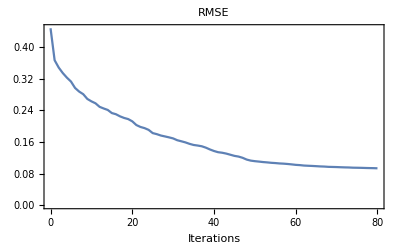

### Training and testing error

As we can see from the graph of the global error - training error is near 0.1
Let’s calculate testing error

```mathematica
100 - (Count[Abs[yTest - Round[net1[xTest]]], {0, 0, 0}] / Length[testData] * 100.0)
```

2.22222

Testing error is quite big form the first look, but we’re calculating it comparing to our expected dataset which isn’t really big. 
But still our model may be a bit overfitted.

### The distribution via classes

We can also look at the distribution via classes on each 20 iterations.

```mathematica
NetPlot[fitrecord,xTrain,yTrain,DataFormat->BarChart,OutputNonlinearity->UnitStep,Intervals->20]
```

-Graphics-

### The confusion matrix

Let’s look at the desired values

```mathematica
yTest
```

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

and actual ones

```mathematica
Round[net1[xTest]]
```

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

and their difference

```mathematica
yTest - Round[net1[xTest]]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,-1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

First, we will calculate the number of correct predictions for each class:

setosa classified as setosa: 15
versicolor classified as versicolor: 14
virginica classified as virginica: 15

Now, we can calculate the number of incorrect predictions for each class:

setosa classified as versicolor: 0
setosa classified as virginica: 0

versicolor classified as  setosa: 0
versicolor classified as  virginica: 1

virginica classified as setosa: 0
virginica classified as versicolor: 0

So now we can plot a matrix:

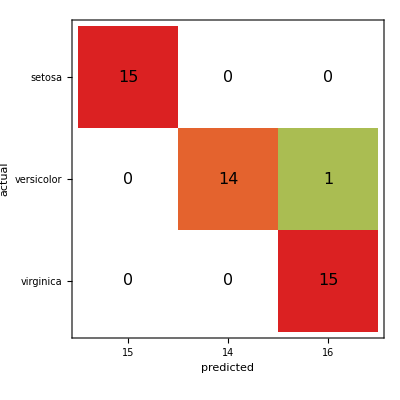

```mathematica
matrix={{15,0,0},{0,14,1},{0,0,15}};
keys={"setosa","versicolor","virginica"};
MatrixPlot[matrix,ColorRules->{0->White},Frame->True,FrameLabel->{"actual","predicted"},FrameTicks->{{MapIndexed[{#2[[1]],#}&,keys],MapIndexed[{#2[[1]],#}&,Total@Transpose@matrix]},{MapIndexed[{#2[[1]],#}&,Total[matrix]],MapIndexed[{#2[[1]],#}&,keys]}},ColorFunction->"Rainbow",Epilog->MapIndexed[Text[Style[#,16],#2-1/2]&,Transpose@Reverse@matrix,{2}]]
```

So as we can see our model got one classification wrong. 

So our model has small enough training and testing errors, got one item wrong, and is just a bit overfitted.

## Initializing of our second fnn(Neuron → Tanh,OutputNonlinearity→SaturatedLinear)

```mathematica
net2=InitializeFeedForwardNet[xTrain,yTrain,{8},Neuron -> Tanh,OutputNonlinearity->SaturatedLinear];
```

```mathematica
{net2,fitrecord}=NeuralFit[net2,xTrain,yTrain,80];
```

### Graph of the global error

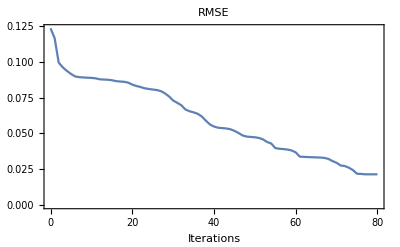

#### Training and testing error

As we can see from the graph of the global error - training error is really small near 0.02
But we can’t say the same about our testing error
Seems like our model suffers a bit from overfitting

```mathematica
100 - (Count[Abs[yTest - Round[net2[xTest]]], {0, 0, 0}] / Length[testData] * 100.0)
```

4.44444

#### The distribution via classes

We can also look at the distribution via classes on each 20 iterations.

```mathematica
NetPlot[fitrecord,xTrain,yTrain,DataFormat->BarChart,OutputNonlinearity->UnitStep,Intervals->20]
```

-Graphics-

#### The confusion matrix

Let’s look at the desired values:

```mathematica
yTest
```

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

and actual ones:

```mathematica
Round[net2[xTest]]
```

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,-1},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

Let’s look at that {0, 1, -1} value

```mathematica
softmax[net2[xTest][[16]]]
```

{0.231839,0.630173,0.137988}

This also decreases our testing error.

Let’s look at the difference between desired and actual values:

```mathematica
yTest - Round[net2[xTest]]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,-1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

First, we will calculate the number of correct predictions for each class:

setosa classified as setosa: 15
versicolor classified as versicolor: 14
virginica classified as virginica: 15

Now, we can calculate the number of incorrect predictions for each class:

setosa classified as versicolor: 0
setosa classified as virginica: 0

versicolor classified as  setosa: 0
versicolor classified as  virginica: 1

virginica classified as setosa: 0
virginica classified as versicolor: 0

So now we can plot a matrix:

```mathematica
matrix={{15,0,0},{0,14,1},{0,0,15}};
keys={"setosa","versicolor","virginica"};
MatrixPlot[matrix,ColorRules->{0->White},Frame->True,FrameLabel->{"actual","predicted"},FrameTicks->{{MapIndexed[{#2[[1]],#}&,keys],MapIndexed[{#2[[1]],#}&,Total@Transpose@matrix]},{MapIndexed[{#2[[1]],#}&,Total[matrix]],MapIndexed[{#2[[1]],#}&,keys]}},ColorFunction->"Rainbow",Epilog->MapIndexed[Text[Style[#,16],#2-1/2]&,Transpose@Reverse@matrix,{2}]]
```

-Graphics-

As we can see our second model is a bit overfitted, because this time we got pretty small training error, but testing error remained the same.

## Initializing of our third fnn(Neuron → Tanh,OutputNonlinearity→SaturatedLinear)

```mathematica
net3=InitializeFeedForwardNet[xTrain,yTrain,{6,4},Neuron -> Tanh,OutputNonlinearity->SaturatedLinear];
```

```mathematica
{net3,fitrecord}=NeuralFit[net3,xTrain,yTrain,60];
```

### Graph of the global error

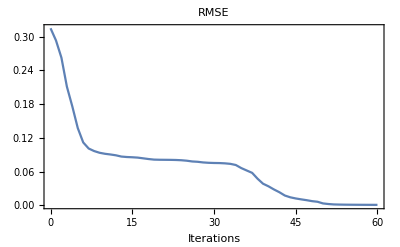

### Training and testing error

As we can see from the graph of the global error - training error is really close to zero
Let’s calculate testing error

```mathematica
100 - (Count[Abs[yTest - Round[net3[xTest]]], {0, 0, 0}] / Length[testData] * 100.0)
```

2.22222

Still our model may suffer from overfitting.

### The distribution via classes

We can also look at the distribution via classes on each 20 iterations.

```mathematica
NetPlot[fitrecord,xTrain,yTrain,DataFormat->BarChart,OutputNonlinearity->UnitStep,Intervals->20]
```

-Graphics-

### The confusion matrix

Let’s look at the desired values:

```mathematica
yTest
```

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

and actual ones:

```mathematica
Round[net3[xTest]]
```

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{1,-1,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

Let’s look closer at a strange output that we got:

```mathematica
net3[xTest][[31]]
```

{0.647426,-0.996199,1.}

This basically means that our item can be classified as first and third cluster. 
Let’s apply softmax function:

```mathematica
softmax[x_]:=N@Exp[x]/Total[Exp[x]];
```

```mathematica
softmax[{0.647426,-0.996199,1.}]
```

{0.382263,0.073883,0.543854}

So we can see that third cluster is the one from 54%. So we can classify it there. But 38% for the first cluster is really close to 54% so this still is a problematic instance.
This also makes our testing error close to zero.

Let’s look at the difference between desired and actual values:

```mathematica
yTest - Round[net3[xTest]]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{-1,1,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

First, we will calculate the number of correct predictions for each class (including our softmax function output):

setosa classified as setosa: 15
versicolor classified as versicolor: 15
virginica classified as virginica: 15

Now, we can calculate the number of incorrect predictions for each class:

setosa classified as versicolor: 0
setosa classified as virginica: 0

versicolor classified as  setosa: 0
versicolor classified as  virginica: 0

virginica classified as setosa: 0
virginica classified as versicolor: 0

So now we can plot a matrix:

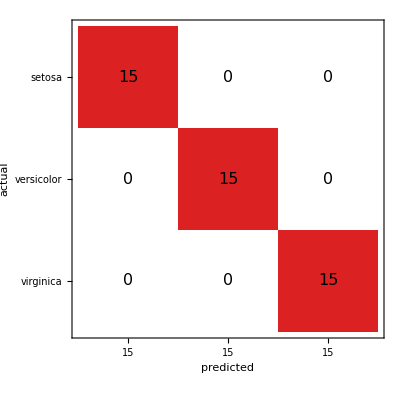

```mathematica
matrix={{15,0,0},{0,15,0},{0,0,15}};
keys={"setosa","versicolor","virginica"};
MatrixPlot[matrix,ColorRules->{0->White},Frame->True,FrameLabel->{"actual","predicted"},FrameTicks->{{MapIndexed[{#2[[1]],#}&,keys],MapIndexed[{#2[[1]],#}&,Total@Transpose@matrix]},{MapIndexed[{#2[[1]],#}&,Total[matrix]],MapIndexed[{#2[[1]],#}&,keys]}},ColorFunction->"Rainbow",Epilog->MapIndexed[Text[Style[#,16],#2-1/2]&,Transpose@Reverse@matrix,{2}]]
```

So basically our last model showed the best results. But we also need not to forget about {1;-1;1} value we got. Even though model got it right, it was still close to classifying it to the first cluster.

So the last model showed to be the best one. It got both training and testing errors close to zero so the model is also not overfitted. 
Seems like 80 iterations may be good to train model well, but may make it a bit overfitted. It’s also a nice practice to play with number of hidden neurons, and output layers.